# Remainders Analysis

```mathematica
(*Preliminaries*)
SetDirectory[FileNameJoin[{NotebookDirectory[],"Data", "PeriodFitData"}] ];

(*Estimated period*)
periodGuess = 0.0337552412;

(*Period formula*)
truePeriod [slope_]:=1/(1/periodGuess-slope) 
σtruePeriod[slopes_,σslopes_]:= 1/(1-slopes)^2*σslopes
```

## 1. Crab 1

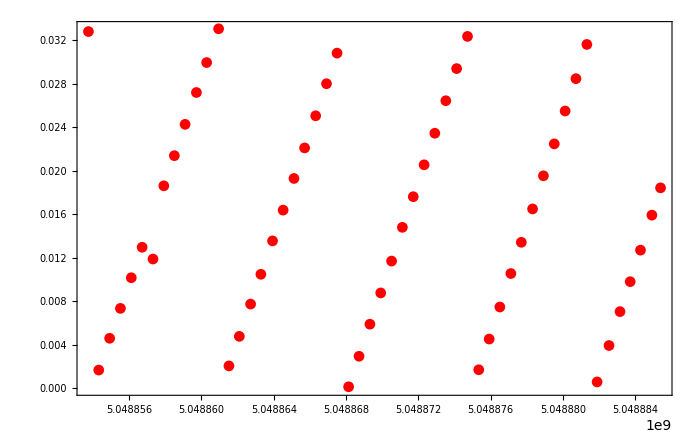

```mathematica
(*Import Data*)
times = ReadList["crab1times.txt", Number];
remainders= ReadList["crab1remainders.txt", Number];

data = Transpose[{times, remainders}];
ListPlot[data, PlotRange->All, Frame->True, ImageSize->700, PlotStyle->{Red, Thick}]
```

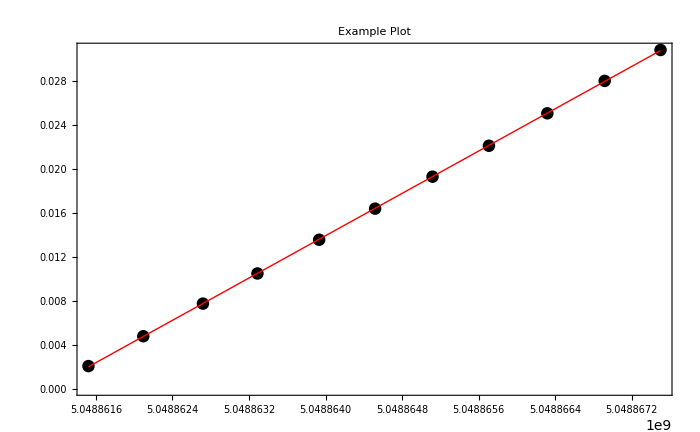

χ^2 values: {0.000014434,1.3868×10^-8,2.3263×10^-8,1.651×10^-8,1.031×10^-8}

Reduced χ^2 values: {1.4434×10^-6,1.5409×10^-9,2.3263×10^-9,1.8344×10^-9,2.062×10^-9}

The probability of getting this χ^2: P = {1.,1.,1.,1.,1.}

```mathematica
(*Separate data into full periods*)
peaksIdxs = FindPeaks[remainders][[All,1]];
sepData =Table[data[[peaksIdxs[[i]]+1;; peaksIdxs[[i+1]]]],{i,1,Length@peaksIdxs - 1}];

(*For each period, find slopes, errors and the residuals*)
slopes = Table[LinearModelFit[sepData[[i]],x,x]["BestFitParameters"][[2]], {i,1,Length@sepData}];
σslopes = Table[LinearModelFit[sepData[[i]],x,x]["ParameterErrors"][[2]], {i,1,Length@sepData}];
residuals = Table[LinearModelFit[sepData[[i]],x,x]["FitResiduals"], {i,1,Length@sepData}];

(*Fit statistics*)
nDof = Table[Length@sepData[[i]]-2,{i,1, Length@sepData}];
χsq = ParallelTable[Total[(residuals[[i]])^2],{i,1,Length@residuals}];
p=ParallelTable[Integrate[(E^(-χs/2)*χs^(nDof[[i]]/2-1))/(2^(nDof[[i]]/2)*Gamma[nDof[[i]]/2]),{χs,χsq[[i]],Infinity}],{i,1, Length@χsq}];
(*Test plot*)
lm = LinearModelFit[sepData[[2]],x,x];
xdata = sepData[[2]][[All,1]];
Show[ListPlot[sepData[[2]],PlotStyle->Black], Plot[lm[x],{x, Min[xdata], Max[xdata]}, PlotRange->All, PlotStyle->{Red, Thick}], Frame->True, ImageSize->700, PlotLabel->"Example Plot", LabelStyle->Directive[20], FrameTicksStyle->{Directive[20],Directive[12]}]

(*Outputting the results*)

Text[Row[{Style["χ^2 values:", Bold]," ", NumberForm[χsq,5]}]] 
Text[Row[{Style["Reduced χ^2 values:", Bold]," ", NumberForm[χsq/nDof,5]}]]  
Text[Row[{Style["The probability of getting this χ^2:", Bold]," P = ",p}]]
```

```mathematica
(*Calculate the periods*)
periods = SetPrecision[truePeriod[slopes],20];
σperiods = SetPrecision[σtruePeriod[slopes,σslopes],20];

(*Compute weighted data*)
wdata = WeightedData[periods, σperiods];
meanPeriod = Mean[wdata];
σmeanPeriod = StandardDeviation[wdata];

Text[Row[{Style["Mean Period:", Bold]," ", NumberForm[meanPeriod,15]}]]
Text[Row[{Style["Error on Mean Period:", Bold]," ", NumberForm[σmeanPeriod,15]}]]
```

Mean Period: 0.0337552466576201

Error on Mean Period: 1.9363337621×10^-10